For input parameters m and n, the number of vertices generated is (m+1)*n/2. This is because of the properties of a hexagonal grid.

```mathematica
nearestHexPoints[point_,coordinates_] := Map[point <-> # &, Nearest[coordinates, point, {7, 2}]][[2;;]]
hexagonalGraphGen[n_, m_] :=Module[{coordinates,edges},
coordinates=Flatten[Table[{i*Sqrt[3],j},{i,1,n},{j,Mod[i, 2],m, 2}], 1];
edges=DeleteDuplicates[Sort /@ Flatten[Map[nearestHexPoints[#,coordinates]&, coordinates], 1]];
Graph[coordinates, edges, VertexCoordinates -> coordinates]
]
```

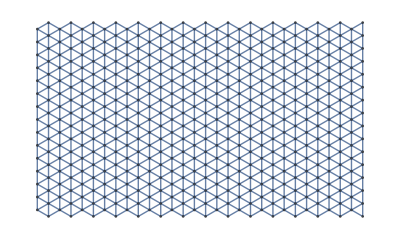

```mathematica
graphRaw=hexagonalGraphGen[30,30]
```

```mathematica
neighbors[graph_Graph, vertex_List] := VertexOutComponent[graph, vertex, 1](*[[2 ;;]]*)
```

```mathematica
neighbors[graphRaw,{Sqrt[3],1}]
```

{{√3,3},{2 √3,0},{2 √3,2}}

```mathematica
labelVerticesByNumber[graph_Graph]:=Fold[Annotate[{#1,#2[[1]]},VertexLabels->ToString[#2[[2]]]]&,graph,Transpose[{VertexList[graph],Range[Length[VertexList[graph]]]}]]
```

```mathematica
groundHeightFunctionFromVertexCoordinate[vertexCoordinate_List]:=vertexCoordinate[[1]]/200.0;
```

```mathematica
waterHeightFunctionFromVertexCoordinate[vertexCoordinate_List]:=0.3;
```

```mathematica
initializeGraph[graph_Graph]:=Fold[
	Annotate[
		{#1,#2[[1]]},(*specifies the graph and the vertex in it to be annotate*)
		"data"->#2[[2]] (*assigns the association in the #2 parameter list as part of the vertex's data attribute*)
	]&,
	graph,
	{#,<|"groundHeight"->groundHeightFunctionFromVertexCoordinate[#],
	"waterLevel"->waterHeightFunctionFromVertexCoordinate[#]|> (*water level is the thickness of water above the ground, not the total height of the surface of the water.*)
	}&/@VertexList[graph]
]
```

```mathematica
graph=initializeGraph[graphRaw];
```

```mathematica
AnnotationValue[{graph,VertexList[graph][[50]]},"data"]["groundHeight"]
```

0.034641

```mathematica
visualizeGraph[graph_Graph]:=SimpleGraph[graph,VertexSize->((#->(AnnotationValue[{graph,#},"data"]["groundHeight"]+AnnotationValue[{graph,#},"data"]["waterLevel"])&)/@VertexList[graph])]
visualizeGraph[graph_Graph,waterLevelSizeWeight_,groundLevelSizeWeight_]:=SimpleGraph[graph,VertexSize->((#->(AnnotationValue[{graph,#},"data"]["groundHeight"]*groundLevelSizeWeight+AnnotationValue[{graph,#},"data"]["waterLevel"]*waterLevelSizeWeight)&)/@VertexList[graph])]
```

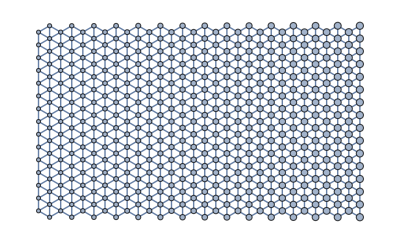

```mathematica
visualizeGraph[graph,1,1]
```

```mathematica
updateCell[graph_Graph,vertex_List]:=Module[{neighborhood,W,H,k=0},
	(*sort neighborhood by ground height*)
	neighborhood=SortBy[neighbors[graph,vertex],AnnotationValue[{graph,#},"data"]["groundHeight"]&];
	
	W=Total[AnnotationValue[{graph,#},"data"]["waterLevel"]&/@neighborhood]; (*calculate the total "volume" of water*)
	Do[
	  Do[
	     tot = tot + h[[i]] - h[[j]];
	     If[tot > W,
	        Return[i - 1]
	     ],
	     {j, 1, i}
	  ],
	  {i, 2, Length[neighborhood]}
	]; (*calculate k*)
	Total[(#1-#2)&]
]
```